```mathematica
SetDirectory[NotebookDirectory[]];
```

Critical temperature (polynomial fit)

```mathematica
Tdata=Import["./muB/muB00/TMeV.dat"];
```

```mathematica
Tlowdata=Import["./CEP/Tlow.dat"];
```

```mathematica
Thighdata=Import["./CEP/Thigh.dat"];
```

```mathematica
pb1=Import["./pb-Nf2p1.dat"];
```

```mathematica
pb=Drop[pb1,1];
```

```mathematica
pb[[1]]
```

{0.,155.672669122307298,171.463193750887399}

```mathematica
mfdata=Import["./muB/muB590/mf.dat"];
```

```mathematica
i=59;
```

```mathematica
Tlow=pb[[i+1,2]];
```

```mathematica
Thigh=pb[[i+1,3]];
```

```mathematica
T0=(Tlow+Thigh)/2;
```

```mathematica
Ttomf=Table[{Tdata[[i,1]],mfdata[[i,1]]},{i,Floor[Tlow],Ceiling[Thigh]}];
```

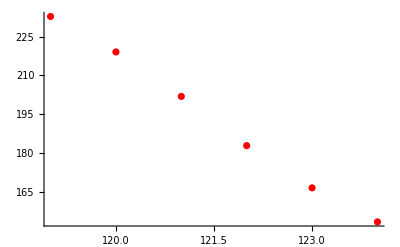

```mathematica
Show[ListPlot[Ttomf,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
lenTtomf=Length[Ttomf];
```

```mathematica
xtomf=Table[{Ttomf[[i,1]]-T0,Ttomf[[i,2]]},{i,lenTtomf}];
```

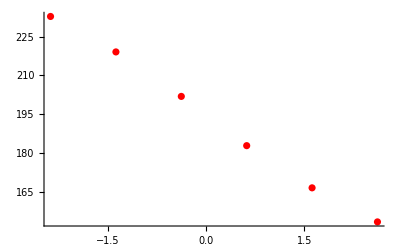

```mathematica
Show[ListPlot[xtomf,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mfFun[T_]=Fit[xtomf,  {1,x,x^2,x^3,x^4},x]/.{x-> T-T0};
```

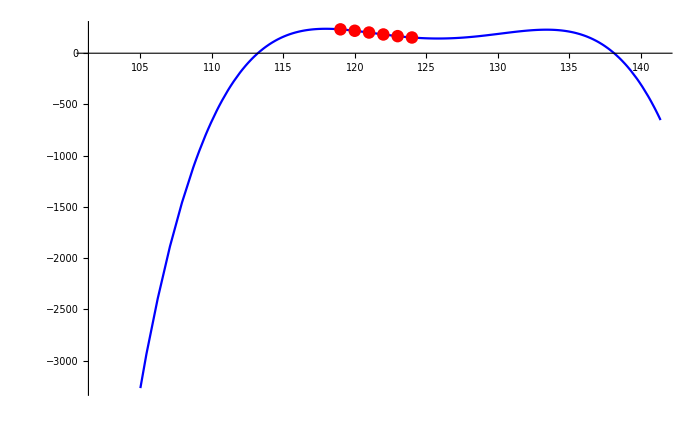

```mathematica
Show[Plot[mfFun[T],{T,T0-20,T0+20},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[Ttomf,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
dmfdT[T_]=D[mfFun[T],T];
```

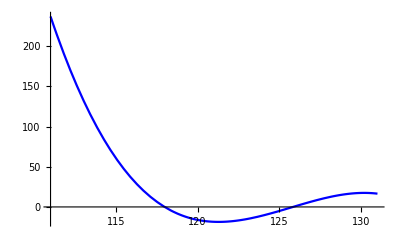

```mathematica
Show[Plot[dmfdT[T],{T,Floor[T0-10],Floor[T0+10]},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
d2mfdT[T_]=D[dmfdT[T],T];
```

```mathematica
FindRoot[d2mfdT[T]==0,{T,T0}]
```

{T→121.286}

```mathematica
121.28605338555083
```

```mathematica
T0
```

121.381920641681091

```mathematica
164.35687088538026 0.951599
```

156.402